# Monte Carlo Method

Adam Rumpf, 9/13/2016

## Introduction

Monte Carlo Methods are a technique for numerical integration. In the 2D case, given a region of interest, the technique consists of drawing a bounding box around the region and then randomly generating points uniformly at random within this box. The proportion of points inside the region of interest should approximate the proportion of the bounding box’s area taken up by the region, and since the box has a known area, we can multiply the proportion by that area to obtain an approximation of the region’s area. As the number of sample points increases, by the Law of Large Numbers, the approximation should approach the true area, although any given realization may vary.

The main functions listed below are mcf[], mcfplot[], mcpi[], and mcpiplot[]. Each accepts a single argument specifying a number of sample points. The two f functions involve calculating the area under an arbitrary test function (which is approximately 0.41338) while the two π functions involve approximating the value of π as the area of a unit circle. Within each set, the first function evaluates the Monte Carlo method once with a specified number of sample points, displaying the approximated area and a plot of the region and points. The second displays a plot of the successive absolute approximation errors resulting from using 1,2,...,n sample points, for a specified value of n. All functions involve random variables and will thus produce different results with each execution.

## Code

### Initialization

```mathematica
(* Arbitrary example curve. *)
f[x_]:=0.6(Sin[2.5Pi x]/(3x+1)-x)+0.65;
(* Monte Carlo method display for function f. The argument specifies the number of sample points. *)
mcf[n_]:=Module[{p,in},
p=RandomReal[1,{n,2}];
in=Total[Boole[(f[#[[1]]]>#[[2]]&)/@p]];
Print["Fraction of Points Under the Curve = ",ToString[N[in/n]]];
Show[RegionPlot[y≤f[x],{x,0,1},{y,0,1}],Graphics[{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],PointSize[100/(4000+5n)],Point[p]}]]
]
(* Lists the successive Monte Carlo approximations for an increasingly-large set of sample points from size 1 to size n. *)
mcflist[n_]:=Module[{p},
p=RandomReal[1,{n,2}];
Table[N[Total[Boole[(f[#[[1]]]>#[[2]]&)/@p[[1;;k]]]]/k],{k,1,n}]
]
(* Display a plot of successive absolute approximation errors. *)
mcfplot[n_]:=ListPlot[Abs[NIntegrate[f[x],{x,0,1}]-mcflist[n]],DataRange->{1,n},AxesLabel->{"samples","abs. error"}]
```

```mathematica
(* Monte Carlo method display for a unit circle. *)
mcpi[n_]:=Module[{p,in},
p=RandomReal[{-1,1},{n,2}];
in=Total[Boole[((#[[1]])^2+(#[[2]])^2≤1&)/@p]];
Print["4 * (Fraction of Points Under the Curve) = ",ToString[N[4in/n]]];
Show[RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}],Graphics[{Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}],PointSize[100/(4000+5n)],Point[p]}]]
]
(* Successive approximation errors *)
mcpilist[n_]:=Module[{p},
p=RandomReal[1,{n,2}];
Table[N[4*Total[Boole[((#[[1]])^2+(#[[2]])^2≤1&)/@p[[1;;k]]]]/k],{k,1,n}]
]
(* Display a plot of successive absolute approximation errors. *)
mcpiplot[n_]:=ListPlot[Abs[Pi-mcpilist[n]],DataRange->{1,n},AxesLabel->{"samples","abs. error"}]
```

### Demonstration

Fraction of Points Under the Curve = 0.43

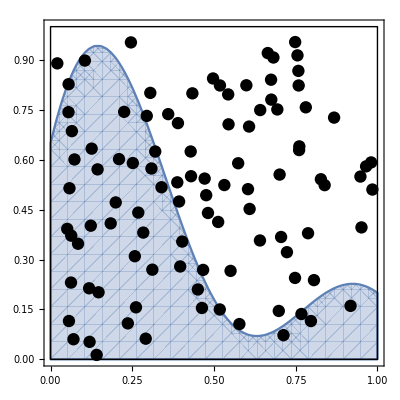

```mathematica
(* Display a realization of the Monte Carlo method applied to an arbitrary test function. 20 sample points, and approximated area. *)
mcf[100]
```

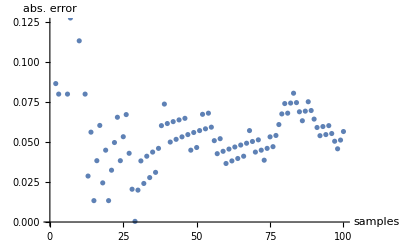

```mathematica
mcfplot[100]
```

4 * (Fraction of Points Under the Curve) = 3.16

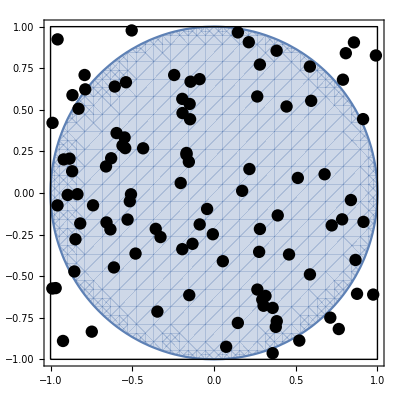

```mathematica
(* Apply the Monte Carlo method to the problem of approximating π as the area of a unit circle. *)
mcpi[100]
```

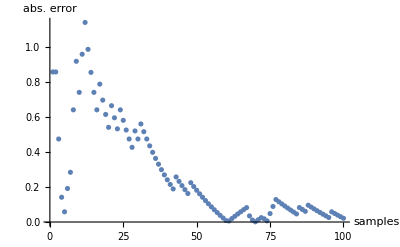

```mathematica
mcpiplot[100]
```